```mathematica
Clear["Global`*"]
```

## Fix the initial conditions you are starting from. a0= semimajor axis [Km], e0 = eccentricity, incl0 = inclination [deg], M0deg = mean anomaly [deg], g0deg = argument of pericenter [deg], h0deg = longitude of nodes [deg]. Fix the initial and final time of integration. t0= initial time [days], tfin = final time [days]

```mathematica
{a0, e0, incl0, M0deg,  g0deg, h0deg} = {RLval + 700,0.111556, 11.2508,  0., 0., 0.};
tin=0;
tfin=1000;
```

## Code importing the normal form solution

### Constants of the problem

```mathematica
GMLval=4.9028001224453001*^3*(24*60*60)^2; (* Moon's G*M parameter[km^3/day^2] *)
GMEval=3.986004407799724*^5 *(24*60*60)^2; (* Earth's G*M parameter[km^3/day^2] *)
RLval= 1738.; (* Radius of the Moon [Km] *)
sostval={GML->GMLval,RL->RLval,GME->GMEval };
Lval=Sqrt[GML*a];
```

### Initial condition (in old/mean variables)

```mathematica
condin0={ain->a0,ein->e0, inclin->incl0*Pi/180, Min->M0deg*Pi/180,  gin->g0deg*Pi/180,hin->h0deg*Pi/180,   I1in->0., I2in->0, I3in->0., I4in->0.,phi1in->0.*Pi/180, phi2in->0.*Pi/180,phi3in->0.*Pi/180,phi4in->0.*Pi/180};
```

### Importing the expression writing the old (mean) variables as function of the new (proper) ones and the frequency used in the homological equation

```mathematica
SetDirectory[NotebookDirectory[]];
heqoldnew = Get["Formule/heqvarold2.wl"];
keqoldnew = Get["Formule/keqvarold2.wl"];
qeqoldnew = Get["Formule/qeqvarold2.wl"];
peqoldnew = Get["Formule/peqvarold2.wl"];
sostfreq = Get["Formule/sostfreq2.wl"];
```

### Importing the solution of the equation of motions in terms of the new (proper) variables

```mathematica
sostsolnew = Get["Formule/sostsolnew.wl"];
```

### Importing the expression writing the new (proper) variables as function of the old (mean) ones. Given initial conditions in the old variables, the following function is needed to compute the initial conditions for the new variables.

```mathematica
condnewin = Get["Formule/condnewin.wl"];
```

### Given the initial value of the semimajor axis a, the following function substitute this value in the expression giving the old variables as function of the new ones: the formula will be in this way shorter and more manageable

```mathematica
simplifyheqkeqqeqpeqanal[condin0_]:=Module[{heqvaroldnew, keqvaroldnew,qeqvaroldnew, peqvaroldnew},
Lin=Lval/.sostval/.a->ain/.condin0;
asin=((Lin^2/GML)/.sostval)/RLval;
heqvaroldnew=Chop[heqoldnew/.sostfreq/.asn->as/.as->asin];
keqvaroldnew=Chop[keqoldnew/.sostfreq/.asn->as/.as->asin];
qeqvaroldnew=Chop[qeqoldnew/.sostfreq/.asn->as/.as->asin];
peqvaroldnew=Chop[peqoldnew/.sostfreq/.asn->as/.as->asin];
Return[{heqvaroldnew,keqvaroldnew,qeqvaroldnew,peqvaroldnew }]]
```

```mathematica
computeanalytical[condin0_]:=Module[{ condnewin1, condnewintot, condnewin2, sostsolnewval, condoldin, heqvaranal, keqvaranal, qeqvaranal, peqvaranal, eanal, ianaldeg, newanalytic},
(* Old values (mean) of the coordinates: *)
condoldin={as->((Lval^2/GML)/.sostval)/RLval/.a->ain, cosi->Cos[inclin], sini->Sin[inclin], e->ein, incl->inclin, eta->Sqrt[1-ein^2],  g->gin, h->hin, I1->I1in, I2->I2in, I3->I3in, I4->I4in, phi1->phi1in, phi2->phi2in,phi3->phi3in,phi4->phi4in }/.condin0;
(* With the change of coordinates giving new coordinates as function of the old ones, we compute the new (proper) initial coordinates*)
condnewin1=Chop[condnewin/.sostfreq/.condoldin];
condnewin2={en0->√(heqvarn0^2+keqvarn0^2), etan0->√(1-heqvarn0^2-keqvarn0^2), cihn0->√(1-peqvarn0^2-qeqvarn0^2), sihn0->√(peqvarn0^2+qeqvarn0^2), gplushn0->ArcTan[heqvarn0,keqvarn0], hn0->ArcTan[qeqvarn0,peqvarn0]}/.condnewin1;
condnewintot=Join[condnewin1, condnewin2];
sostsolnewval=sostsolnew/.condnewintot;
newanalytic=simplifyheqkeqqeqpeqanal[condin0];
heqvaranal=Chop[newanalytic[[1]]/.sostsolnewval];
keqvaranal=Chop[newanalytic[[2]]/.sostsolnewval];
qeqvaranal=Chop[newanalytic[[3]]/.sostsolnewval];
peqvaranal=Chop[newanalytic[[4]]/.sostsolnewval];
eanal=Sqrt[Chop[Expand[heqvaranal^2+keqvaranal^2]]];
ianaldeg=2*ArcSin[Sqrt[Chop[Expand[qeqvaranal^2+peqvaranal^2]]]]*180./Pi;
Return[{eanal, ianaldeg}]
]
```

```mathematica
ploteccinclanalytical[condin0_, tin_, tfin_]:=Module[{ eianal, eanal, ianaldeg, pleanal,plianaldeg},
eianal=computeanalytical[condin0];
eanal=eianal[[1]];
ianaldeg=eianal[[2]];
pleanal=Plot[eanal, {t, tin, tfin}, ImageSize->Large, PlotStyle->Red,AxesLabel->{Style["t", Bold, 20, Black],Style["e", Bold, 20, Black]}, LabelStyle->Directive[Bold,20]];
plianaldeg=Plot[ianaldeg, {t, tin, tfin}, ImageSize->Large, PlotStyle->Red, AxesLabel->{Style["t", Bold, 20, Black],Style["i°", Bold, 20, Black]},LabelStyle->Directive[Bold,20]];
Return[{pleanal, plianaldeg}]
]
```

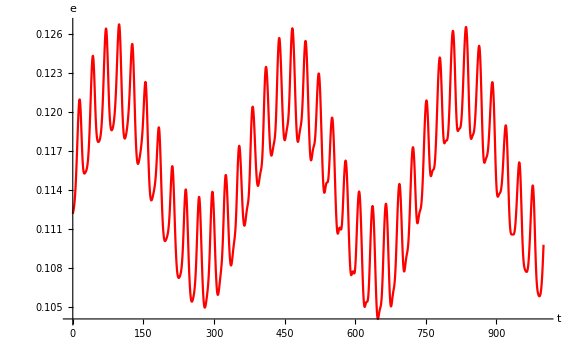
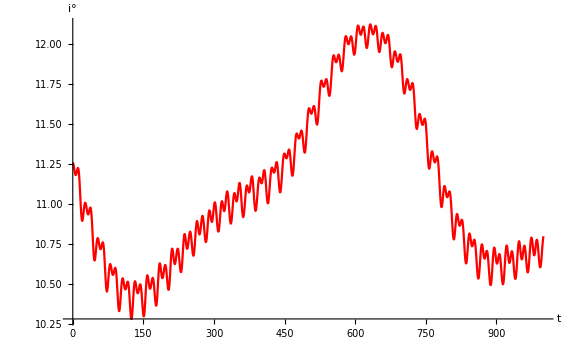

```mathematica
ploteccinclanalytical[condin0, tin, tfin]
```